```mathematica
Needs["ErrorBarPlots`"];
location = "/home/jhell/research/results/batchJobs/mainRuns/attempt6b2/";
flowData =Table[Import[location<>"overallData/overallData"<>ToString[index]<>".dat", "Data"],{index,0, 11}];
concData =Table[Import[location<>"grandConcData/grandConcData"<>ToString[index]<>".dat", "Data"],{index,0, 11}];
lambdaTable  = Table[(1.2-0.05)/11 index+0.05, {index, 0, 11}];
finalData = Table[{concData[[index]]ᵀ[[2]], flowData[[index]]ᵀ[[2]], flowData[[index]]ᵀ[[3]]}ᵀ,{index, 1, 12}];
Manipulate[Grid[{Show[{ErrorListPlot[flowData[[index]],ImageSize->Large, PlotStyle->AbsolutePointSize[1], PlotRange->{{0,1},{0,1.4}}, PlotLegends->"λ = "<>ToString[lambdaTable[[index]]]], Plot[1+(1-lambdaTable[[index]]) ρ (-4+3 ρ), {ρ, 0, 1}, PlotRange->{{0,1}, {0, 1.4}}, ImageSize->Large]}], ErrorListPlot[concData[[index]], PlotRange->{{0,1},{0,1}}, ImageSize->Medium]}], {index, 1, 12, 1}]
```

```mathematica
Manipulate[Show[{ErrorListPlot[finalData[[index]],ImageSize->Large, PlotStyle->AbsolutePointSize[1], PlotRange->{{0,1},{0,1.4}}, PlotLegends->"λ = "<>ToString[lambdaTable[[index]]]], Plot[1+(1-lambdaTable[[index]]) ρ (-4+3 ρ), {ρ, 0, 1}, PlotRange->{{0,1}, {0, 1.4}}, ImageSize->Large]}], {index, 1, 12, 1}]
```

```mathematica
Needs["ErrorBarPlots`"];
location = "/home/jhell/research/results/batchJobs/mainRuns/attempt6b2/";
flowData =Table[Import[location<>"overallData/overallData"<>ToString[index]<>".dat", "Data"],{index,0, 11}];
lambdaTable  = Table[(1.2-0.05)/11 index+0.05, {index, 0, 11}];
Manipulate[Show[{ErrorListPlot[flowData[[index]],ImageSize->Large, PlotStyle->AbsolutePointSize[1], PlotRange->{{0,1},{0,1.4}}, PlotLegends->"λ = "<>ToString[lambdaTable[[index]]]], Plot[1+(1-lambdaTable[[index]]) ρ (-4+3 ρ), {ρ, 0, 1}, PlotRange->{{0,1}, {0, 1.4}}, ImageSize->Large]}], {index, 1, 12, 1}]
```

```mathematica
f[x_] := 0;
set1 = Transpose[concData[[1]]]
set8 = Transpose[concData[[8]]]
set8[[1]]-set1[[1]]
reassData = Transpose[{set1[[1]], set1[[1]], Array[f, Length[set1[[1]]]]}];
oldFragment = Table[concData[[index]], {index, 1, 7}];
series8 = {Transpose[{set8[[1]], set8[[1]], Array[f, Length[set8[[1]]]]}]};
newPadding = Table[reassData, {index, 9, 12}];
newConcData = Join[oldFragment, series8, newPadding];
Manipulate[Grid[{Show[{ErrorListPlot[flowData[[index]],ImageSize->Large, PlotStyle->AbsolutePointSize[1], PlotRange->{{0,1},{0,1.4}}, PlotLegends->"λ = "<>ToString[lambdaTable[[index]]]], Plot[1+(1-lambdaTable[[index]]) ρ (-4+3 ρ), {ρ, 0, 1}, PlotRange->{{0,1}, {0, 1.4}}, ImageSize->Large]}], ErrorListPlot[newConcData[[index]], PlotRange->{{0,1},{0,1}}, ImageSize->Medium]}], {index, 1, 12, 1}]
finalData = Table[{newConcData[[index]]ᵀ[[2]], flowData[[index]]ᵀ[[2]], flowData[[index]]ᵀ[[3]]}ᵀ,{index, 1, 12}];
contourData = Flatten[Table[{newConcData[[index]]ᵀ[[2]], Table[lambdaTable[[index]], {j, 1, Length[newConcData[[index]]ᵀ[[2]]]}], flowData[[index]]ᵀ[[2]]}ᵀ,{index, 1, 12}], 1];
pointsData = Flatten[Table[{newConcData[[index]]ᵀ[[2]], Table[lambdaTable[[index]], {j, 1, Length[newConcData[[index]]ᵀ[[2]]]}]}ᵀ,{index, 1, 12}], 1];
Manipulate[Show[{ErrorListPlot[finalData[[index]],ImageSize->Large, PlotStyle->AbsolutePointSize[1], PlotRange->{{0,1},{0,1.4}}, PlotLegends->"λ = "<>ToString[lambdaTable[[index]]]], Plot[1+(1-lambdaTable[[index]]) ρ (-4+3 ρ), {ρ, 0, 1}, PlotRange->{{0,1}, {0, 1.4}}, ImageSize->Large]}], {index, 1, 12, 1}]
```

{{0.316087,0.888261,0.275217,0.152609,0.479565,0.806522,0.602174,0.724783,0.234348,0.111739,0.97,0.193478,0.0708696,0.561304,0.03,0.683913,0.92913,0.847391,0.397826,0.520435,0.643043,0.438696,0.356957,0.765652},{0.959516,0.959683,0.951627,0.894255,0.967964,0.962917,0.969692,0.967642,0.944534,0.82025,0.976847,0.925046,0.49811,0.970029,0.082444,0.968267,0.963089,0.961956,0.957485,0.967871,0.96895,0.968374,0.961793,0.966954},{0.00603248,0.0058331,0.00641677,0.0114302,0.00533266,0.00559677,0.00513517,0.00465994,0.00833547,0.0146966,0.00397348,0.00960723,0.0209641,0.00459851,0.00896417,0.00520548,0.00542824,0.00561332,0.0197778,0.00537779,0.00470808,0.00487437,0.00539434,0.0049739}}

{{0.316087,0.888261,0.275217,0.152609,0.479565,0.806522,0.602174,0.724783,0.234348,0.111739,0.193478,0.0708696,0.561304,0.03,0.683913,0.92913,0.847391,0.397826,0.520435,0.643043,0.438696,0.356957,0.765652},{0.313203,0.494849,0.26942,0.151873,0.469195,0.796664,0.594871,0.722017,0.239596,0.11399,0.193457,0.0736652,0.554326,0.036326,0.672272,0.375218,0.839555,0.389989,0.513282,0.639402,0.428803,0.355127,0.757579},{0.00966867,0.0732773,0.00928586,0.0079419,0.0115891,0.0179119,0.011039,0.0109451,0.00918844,0.00644242,0.00845695,0.00534061,0.0106492,0.00358764,0.0106595,0.0406369,0.00850677,0.010343,0.0104807,0.0107737,0.0106136,0.0104515,0.0100631}}

Thread::tdlen: Objects of unequal length in {0.316087,0.888261,0.275217,0.152609,0.479565,0.806522,0.602174,0.724783,0.234348,0.111739,0.193478,0.0708696,0.561304,0.03,0.683913,0.92913,0.847391,0.397826,0.520435,0.643043,0.438696,0.356957,0.765652}+{-0.316087,-0.888261,-0.275217,-0.152609,-0.479565,-0.806522,-0.602174,-0.724783,«8»,-0.92913,-0.847391,-0.397826,-0.520435,-0.643043,-0.438696,-0.356957,-0.765652} cannot be combined.

{0.316087,0.888261,0.275217,0.152609,0.479565,0.806522,0.602174,0.724783,0.234348,0.111739,0.193478,0.0708696,0.561304,0.03,0.683913,0.92913,0.847391,0.397826,0.520435,0.643043,0.438696,0.356957,0.765652}+{-0.316087,-0.888261,-0.275217,-0.152609,-0.479565,-0.806522,-0.602174,-0.724783,-0.234348,-0.111739,-0.97,-0.193478,-0.0708696,-0.561304,-0.03,-0.683913,-0.92913,-0.847391,-0.397826,-0.520435,-0.643043,-0.438696,-0.356957,-0.765652}

```mathematica
newConcData[[8]]ᵀ[[2]]
flowData[[8]]ᵀ[[2]]
flowData[[8]]ᵀ[[3]]
```

{0.316087,0.888261,0.275217,0.152609,0.479565,0.806522,0.602174,0.724783,0.234348,0.111739,0.193478,0.0708696,0.561304,0.03,0.683913,0.92913,0.847391,0.397826,0.520435,0.643043,0.438696,0.356957,0.765652}

{0.791749,0.739991,0.799193,0.848416,0.751385,0.717856,0.68721,0.725055,0.796042,0.876376,0.822836,0.891838,0.727719,0.935143,0.725873,0.757943,0.734051,0.750813,0.736783,0.728853,0.737493,0.757153,0.723984}

{0.00892076,0.00564798,0.00841352,0.00692757,0.0152953,0.00914683,0.00971913,0.0135194,0.00881501,0.00708405,0.00909469,0.00689717,0.0132107,0.00148691,0.00874602,0.00254911,0.00640527,0.0140834,0.0127383,0.0172646,0.0221661,0.0176316,0.0121195}

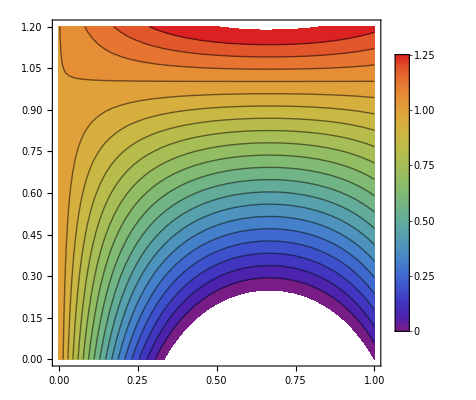

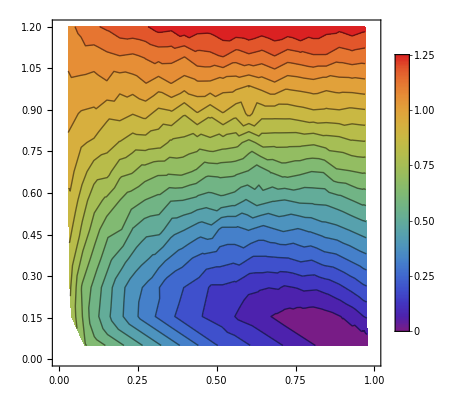

-Graphics3D-

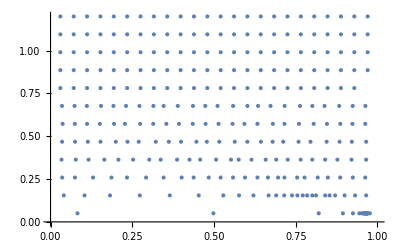

```mathematica
ContourPlot[1+(1-λ) ρ (-4+3 ρ), {ρ, 0, 1}, {λ, 0, 1.2}, PlotRange->{0, 1.25}, Contours->20, ColorFunction->"Rainbow", PlotLegends->Automatic]
ListContourPlot[contourData, PlotRange->{{0, 1}, {0, 1.2}, {0, 1.25}}, InterpolationOrder->3, Contours->20, ColorFunction->"Rainbow", PlotLegends->Automatic]
ListPointPlot3D[contourData, PlotRange->{{0, 1}, {0, 1.2}, {0, 1.2}}]
ListPlot[pointsData, PlotRange->{{0, 1}, {0, 1.2}}]
```